```mathematica
PacletDirectoryLoad["/Users/pthevena/Desktop/SplineKit/SplineKit"];
Needs["SplineKit`PeriodicSplines`"]
Names["SplineKit`PeriodicSplines`*"]
```

{AreaUnderPβ,DegreePβ,DelayPβ,ExtremaPβ,FourierCoeffPβ,fPβ,MeanPβ,PeriodPβ,PβAntiGrad,PβConvolvePβ,PβDelayed,PβDiff,PβDownscaledProjected,PβFromCoeffβ,PβFromSamples,PβGrad,PβLowerBoundPβ,PβNegated,PβNormedCrossCorrPβ,PβPlusPβ,PβPlusPβProjected,PβPlusScalar,PβProjected,PβQ,PβRescaledProjected,PβReversed,PβTimesScalar,PβUpperBoundPβ,PβUpscaled,PβUpscaledProjected,PβWithFractionalDelay,SamplesFromPβ,SgnPβ,ShowPβ,VariancePβ,ZeroCrossPβ,ZeroesPβ}

```mathematica
maxDegree=11
minTests=10
```

11

10

```mathematica
(* from_samples _unregularized_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,False,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->False]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* from_samples _unregularized_ _integer_delay_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}]},{n,Δx,False,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->False]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* from_samples _unregularized_ _odd_period_ _half_integer_delay_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],2K-1],Δx=0.5+RandomInteger[{-n-2,n+2}]},{n,Δx,False,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->False]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* from_samples _regularized_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,True,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->True]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* from_samples _regularized_ _integer_delay_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}]},{n,Δx,True,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->True]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* from_samples _regularized_ _half_integer_delay_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{ƒ=RandomVariate[NormalDistribution[],K],Δx=0.5+RandomInteger[{-n-2,n+2}]},{n,Δx,True,Map[CForm,ƒ],Map[CForm,PβFromSamples[ƒ,n,Delay->Δx,Regularized->True]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* at *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβFromCoeffβ[c,n,Δx],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* at _extended_zeroes_*)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Block[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],x0=RandomInteger[{0,K-1}],w0=RandomInteger[{1,3}],k},For[k=x0,k<x0+n+w0,k++,c[[Mod[k,K]+(1)]]=0];{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβFromCoeffβ[c,n,Δx],#]},0.0+Chop[y]//CForm]&,x],"\r"}],{K,2(n+1)+5,2(n+1)+10}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* at _half_integers_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}] ,x=Table[0.5k,{k,2(-n-1-4)-1,2(K-1+n+1+4)+1}]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβFromCoeffβ[c,n,Δx],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* at _half_integers_ _midpoint_zeroes_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Block[{k,c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}] ,x=Table[0.5k,{k,2(-n-1-4)-1,2(K-1+n+1+4)+1}],p=Table[RandomInteger[{0,K-1}],2]},For[k=0,k<Length[p],k++,c[[p[[k+(1)]]+(1)]]=-c[[Mod[p[[k+(1)]]+1,K]+(1)]]];{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβFromCoeffβ[c,n,Δx],#]},y//CForm]&,x],"\r"}],{K,{2,2,2,2,2,3,3,3,3,3,4,4,4,4,4,5,5,5,5,5,6,6,6,6,6,7,7,7,7,7}}],{n,0,0}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* get_samples *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K+minTests]]},{n,Δx,Map[CForm,c],B,M,x,Map[CForm,SamplesFromPβ[PβFromCoeffβ[c,n,Δx],B,M,x]],"\r"}],{M,1,5}],{B,1,5}],{K,1,n+1+4}],{n,0,3}],3]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* get_samples _half_integers_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}],x=0.5+RandomInteger[{2(-n-1-4)-1,2(K-1+n+1+4)+1}]},{n,Δx,Map[CForm,c],B,M,x,Map[CForm,SamplesFromPβ[PβFromCoeffβ[c,n,Δx],B,M,x]],"\r"}],{M,1,2}],{B,1,5}],{K,1,n+1+4}],{n,0,3}],3]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* mean *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],MeanPβ[PβFromCoeffβ[c,n,Δx]]//CForm,"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* variance *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],VariancePβ[PβFromCoeffβ[c,n,Δx]]//CForm,"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* integrate *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],ab=RandomVariate[NormalDistribution[0.5*(K-1),K+minTests],{5,2}]},{n,Δx,Map[CForm,c],Table[Map[CForm,ab[[k]]],{k,Length[ab]}],Table[Map[CForm,AreaUnderPβ[PβFromCoeffβ[c,n,Δx],ab[[k]]]],{k,Length[ab]}],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* lower_bound *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβLowerBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,5},{n,0,5}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* lower_bound_half_integer *)
CopyToClipboard[StringReplace[ToString[Flatten[Join[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}],x=0.5+RandomInteger[{2(-n-1-4)-1,2(K-1+n+1+4)+1},K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβLowerBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,0},{n,0,5}],Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}],x=0.5+RandomInteger[{2(-n-1-4)-1,2(K-1+n+1+4)+1},K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβLowerBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,5},{n,0,0}]],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* upper_bound *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβUpperBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,5},{n,0,5}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* upper_bound_half_integer *)
CopyToClipboard[StringReplace[ToString[Flatten[Join[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}],x=0.5+RandomInteger[{2(-n-1-4)-1,2(K-1+n+1+4)+1},K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβUpperBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,0},{n,0,5}],Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomInteger[{-n-2,n+2}],x=0.5+RandomInteger[{2(-n-1-4)-1,2(K-1+n+1+4)+1},K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβUpperBoundPβ[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,5},{n,0,0}]],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
PolyPβ[s_/;PβQ[s]]:=With[{c=s["c"],n=s["n"],Δx=s["Δx"],P=Length[s["c"]]},Block[{x},If[1==P,{{{Δx,Δx+1},c[[0+(1)]]}},If[0==n,Flatten[Join[{{{Δx-1/2,(Last[c]+First[c])/2},{{Δx-1/2,Δx+1/2},First[c]}}},Array[{{#+Δx-1/2,(c[[#-1+(1)]]+c[[#+(1)]])/2},{{#+Δx-1/2,#+Δx+1/2},c[[#+(1)]]}}&,P-1,1]],1],Block[{px=SplineKit`SplineUtilities`Private`Wβ[n].First[VandermondeMatrix[{x},n+1]]},Flatten[Array[With[{min=#+Δx+(n-1)/2,max=#+Δx+(n+1)/2},{{{min,max},Array[c[[Mod[#,P]+(1)]]&,n+1,#].px}}]&,P,0],1]]]]]];
```

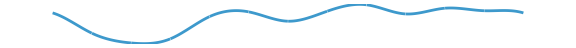

```mathematica
With[{c=RandomVariate[NormalDistribution[],#2],Δx=RandomVariate[NormalDistribution[]]},With[{min=Min[ExtremaPβ[PβFromCoeffβ[c,#1,Δx]][[All,2]]],max=Max[ExtremaPβ[PβFromCoeffβ[c,#1,Δx]][[All,2]]]},GraphicsColumn[{Plot[fPβ[PβFromCoeffβ[c,#1,Δx],x+Δx+(#1-1)/2],{x,0,#2},PlotRange->{min,max},Axes->None,ImageSize->Large,AspectRatio->(1/#2)9/16],GraphicsRow[Map[Plot[#[[2]],{x,0,1},PlotRange->{{0,1},{min,max}},Axes->None]&,Select[{c,Expand[PolyPβ[PβFromCoeffβ[c,#1,Δx]]]}[[2]],ListQ[#[[1]]]&]],0,ImageSize->Large,AspectRatio->9/16]}]]]&[3,12]
```

```mathematica
(* piecewise_polynomials *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],Map[CForm,Expand[PolyPβ[PβFromCoeffβ[c,n,Δx]]]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]","("->"[",")"->"]","List("->"[",RegularExpression["Power\\(x,([0123456789]*)\\)"]:>"(x**$1)",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zeroes _easy_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[With[{nz=RandomInteger[{1,n}]},With[{partition=RandomChoice[IntegerPartitions[nz,All,Table[k,{k,1,nz,2}]]]},With[{z=Transpose[{partition,Sort[Table[RandomReal[{0,1}],{k,Length[partition]}]]}],p0=Table[RandomVariate[NormalDistribution[]],n+1-nz]},With[{p=FromDigits[p0,#]∏_(k=1)^Length[z] (#-z[[k,2]])^z[[k,1]]&},Module[{x},With[{c=CoefficientList[p[x],x].SplineKit`SplineUtilities`Private`InvWβ[n]},With[{f=PβFromCoeffβ[c,n,RandomReal[{-2.0,2.0}]]},{n,DelayPβ[f],Map[CForm,c],Map[CForm,Mod[z[[All,2]]+(3n+1)/2+DelayPβ[f],n+1]],Map[CForm,Mod[z[[All,1]],n+1]],Map[CForm,Mod[Select[ZeroesPβ[f],NumberQ],n+1]],"\r"}]]]]]]],{n,1,maxDegree},{20}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zeroes *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[With[{nz=RandomInteger[{1,n}]},With[{partition=IntegerPartitions[nz][[RandomInteger[{1,PartitionsP[nz]}]]]},With[{z=Transpose[{partition,Sort[Table[RandomReal[{0,1}],{k,Length[partition]}]]}],p0=Table[RandomVariate[NormalDistribution[]],n+1-nz]},With[{p=FromDigits[p0,#]∏_(k=1)^Length[z] (#-z[[k,2]])^z[[k,1]]&},Module[{x},With[{c=CoefficientList[p[x],x].SplineKit`SplineUtilities`Private`InvWβ[n]},With[{f=PβFromCoeffβ[c,n,RandomReal[{-2.0,2.0}]]},{n,DelayPβ[f],Map[CForm,c],Map[CForm,Mod[z[[All,2]]+(3n+1)/2+DelayPβ[f],n+1]],Map[CForm,Mod[z[[All,1]],n+1]],Map[CForm,Mod[Select[ZeroesPβ[f],NumberQ],n+1]],"\r"}]]]]]]],{n,1,maxDegree},{20}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zeroes _hard_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[With[{Nz=RandomInteger[{1,n}]},With[{partition=IntegerPartitions[Nz][[RandomInteger[{1,PartitionsP[Nz]}]]]},With[{z=DeleteDuplicates[Transpose[{partition,Sort[Table[RandomChoice[Table[ρ,{ρ,0,1,1/10}]],{k,Length[partition]}]]}],#1[[2]]==#2[[2]]&]},With[{nz=Total[z[[All,1]]]},With[{p0=Table[1/2 RandomChoice[{-5,-4,-3,-2,-1,1,2,3,4,5}],n+1-nz]},With[{p=FromDigits[p0,#]∏_(k=1)^Length[z] (#-z[[k,2]])^z[[k,1]]&},With[{c=Map[Rationalize[#,10^-3]&,CoefficientList[p[x],x].SplineKit`SplineUtilities`Private`InvWβ[n]]},With[{C=c/Apply[GCD,c]},With[{f=PβFromCoeffβ[C,n,1/5 RandomInteger[{-n-2,n+2}]]},{n,0.0+DelayPβ[f],Map[CForm,C],Map[CForm,0.0+Mod[z[[All,2]]+(3n+1)/2+DelayPβ[f],n+1]],Map[CForm,Mod[z[[All,1]],n+1]],Map[CForm,Mod[Select[ZeroesPβ[f],NumberQ],n+1]],"\r"}]]]]]]]]],{n,1,maxDegree},{20}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zero_crossings _degree0_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Module[{x},With[{c=0.0+RandomInteger[{-1,1},RandomInteger[{1,20}]]},With[{f=PβFromCoeffβ[c,0,RandomChoice[{RandomReal[{-2.0,2.0}],RandomReal[{-2.0,2.0}],RandomReal[{-2.0,2.0}],-0.5,0.0,0.5}]]},With[{azc=If[0==Chop[Max[#]-Min[#]],CForm[(Min[#]+Max[#])/2],{CForm[Min[#]],CForm[Max[#]]}]&/@ZeroCrossPβ[f, Ascending->True, Descending->False],dzc=If[0==Chop[Max[#]-Min[#]],CForm[(Min[#]+Max[#])/2],{CForm[Min[#]],CForm[Max[#]]}]&/@ZeroCrossPβ[f, Ascending->False, Descending->True]},{0,DelayPβ[f],Map[CForm,c],azc,dzc,"\r"}]]]],{200}],0]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zero_crossings _easy_ *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[With[{nz=RandomInteger[{1,n}]},With[{partition=RandomChoice[IntegerPartitions[nz,All,Table[k,{k,1,nz,2}]]]},With[{z=Transpose[{partition,Sort[Table[RandomReal[{0,1}],{k,Length[partition]}]]}],p0=Table[RandomVariate[NormalDistribution[]],n+1-nz]},With[{p=FromDigits[p0,#]∏_(k=1)^Length[z] (#-z[[k,2]])^z[[k,1]]&},Module[{x},With[{c=CoefficientList[p[x],x].SplineKit`SplineUtilities`Private`InvWβ[n]},With[{f=PβFromCoeffβ[c,n,RandomReal[{-2.0,2.0}]]},With[{azc=Sort[Map[If[0==Chop[Min[#]-Max[#]],Mod[(Min[#]+Max[#])/2,Length[f["c"]]],Mod[{Min[#],Max[#]},Length[f["c"]]]]&,ZeroCrossPβ[f, Ascending->True, Descending->False]]],dzc=Sort[Map[If[0==Chop[Min[#]-Max[#]],Mod[(Min[#]+Max[#])/2,Length[f["c"]]],Mod[{Min[#],Max[#]},Length[f["c"]]]]&,ZeroCrossPβ[f, Ascending->False, Descending->True]]]},{n,DelayPβ[f],Map[CForm,c],Map[CForm,0.0+Mod[z[[All,2]]+(3n+1)/2+DelayPβ[f],n+1]],Map[CForm,Mod[z[[All,1]],n+1]],Map[CForm,azc],Map[CForm,dzc],"\r"}]]]]]]]],{n,1,maxDegree},{20}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* pointwise_zero_crossings *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[With[{nz=RandomInteger[{1,n}]},With[{partition=IntegerPartitions[nz][[RandomInteger[{1,PartitionsP[nz]}]]]},With[{z=Transpose[{partition,Sort[Table[RandomReal[{0,1}],{k,Length[partition]}]]}],p0=Table[RandomVariate[NormalDistribution[]],n+1-nz]},With[{p=FromDigits[p0,#]∏_(k=1)^Length[z] (#-z[[k,2]])^z[[k,1]]&},Module[{x},With[{c=CoefficientList[p[x],x].SplineKit`SplineUtilities`Private`InvWβ[n]},With[{f=PβFromCoeffβ[c,n,RandomReal[{-2.0,2.0}]]},With[{azc=Sort[Map[If[0==Chop[Min[#]-Max[#]],Mod[(Min[#]+Max[#])/2,Length[f["c"]]],Mod[{Min[#],Max[#]},Length[f["c"]]]]&,ZeroCrossPβ[f, Ascending->True, Descending->False]]],dzc=Sort[Map[If[0==Chop[Min[#]-Max[#]],Mod[(Min[#]+Max[#])/2,Length[f["c"]]],Mod[{Min[#],Max[#]},Length[f["c"]]]]&,ZeroCrossPβ[f, Ascending->False, Descending->True]]]},{n,DelayPβ[f],Map[CForm,c],Map[CForm,0.0+Mod[z[[All,2]]+(3n+1)/2+DelayPβ[f],n+1]],Map[CForm,Mod[z[[All,1]],n+1]],Map[CForm,azc],Map[CForm,dzc],"\r"}]]]]]]]],{n,1,maxDegree},{20}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* extrema *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],With[{min=ExtremaPβ[PβFromCoeffβ[c,n,Δx],Minima->True,Maxima->False],max=ExtremaPβ[PβFromCoeffβ[c,n,Δx],Minima->False,Maxima->True]},{Switch[Head[#[[1]]],List,#,Interval,If[Min[#[[1]]]==Max[#[[1]]],{Min[#[[1]]],#[[2]]},{{Min[#[[1]]],Max[#[[1]]]},#[[2]]}]]&/@min,Switch[Head[#[[1]]],List,#,Interval,If[Min[#[[1]]]==Max[#[[1]]],{Min[#[[1]]],#[[2]]},{{Min[#[[1]]],Max[#[[1]]]},#[[2]]}]]&/@max}],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* Fourier_coeff *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],ν=RandomInteger[{-2K,3K},K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,ν],Map[With[{y=FourierCoeffPβ[PβFromCoeffβ[c,n,Δx],#]},y//CForm]&,ν],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* fractionalized_delay *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβWithFractionalDelay[PβFromCoeffβ[c,n,Δx]],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* delayed_by *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],τ=RandomVariate[NormalDistribution[0.0, 2.0]]},{n,Δx,τ,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβDelayed[PβFromCoeffβ[c,n,Δx],τ],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* mirrored *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβReversed[PβFromCoeffβ[c,n,Δx]],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* plus *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],c0=RandomVariate[NormalDistribution[0.0, 2.0]]},{n,Δx,c0,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβPlusScalar[PβFromCoeffβ[c,n,Δx],c0],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* negated *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβNegated[PβFromCoeffβ[c,n,Δx]],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* times *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[0.0, 2.0]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],λ=RandomVariate[NormalDistribution[0.0, 2.0]]},{n,Δx,λ,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβTimesScalar[PβFromCoeffβ[c,n,Δx],λ],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* gradient *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],Map[CForm,PβGrad[PβFromCoeffβ[c,n,Δx]]["n"]],Map[CForm,PβGrad[PβFromCoeffβ[c,n,Δx]]["Δx"]],Map[CForm,PβGrad[PβFromCoeffβ[c,n,Δx]]["c"]],"\r"}],{K,1,n+1+4}],{n,1,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* anti_grad *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]]},{n,Δx,Map[CForm,c],Map[CForm,PβAntiGrad[PβFromCoeffβ[c,n,Δx]]["n"]],Map[CForm,PβAntiGrad[PβFromCoeffβ[c,n,Δx]]["Δx"]],Map[CForm,PβAntiGrad[PβFromCoeffβ[c,n,Δx]]["c"]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* differentiated *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβDiff[PβFromCoeffβ[c,n,Δx],m],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{m,0,n}],{n,0,5}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* projected *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],δx=RandomVariate[NormalDistribution[],K+minTests]},{n,m,Δx,Map[CForm,c],Map[CForm,x],Map[CForm,δx],Map[With[{y=fPβ[PβProjected[PβFromCoeffβ[c,n,Δx],{m,Last[#]}],First[#]]},y//CForm]&,Transpose[{x,δx}]],"\r"}],{K,1,n+1+4}],{m,0,5}],{n,0,5}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* upscaled *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(M K-1),M K],K+minTests]},{n,M,Δx,Map[CForm,c],Map[CForm,x],Map[With[{y=fPβ[PβUpscaled[PβFromCoeffβ[c,n,Δx],M],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{M,1,5}],{n,0,maxDegree}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* upscaled_projected *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(M K-1),M K],K+minTests],δx=RandomVariate[NormalDistribution[],K+minTests],p=RandomInteger[{0,maxDegree},K+minTests]},{n,M,Δx,Map[CForm,c],Map[CForm,x],Map[CForm,δx],Map[CForm,p],Map[With[{y=fPβ[PβUpscaledProjected[PβFromCoeffβ[c,n,Δx],M,{#[[3]],#[[2]]}],#[[1]]]},y//CForm]&,Transpose[{x,δx,p}]],"\r"}],{K,1,n+1+4}],{M,1,5}],{n,0,maxDegree}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* downscaled_projected *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(M K-1),M K],K+minTests],δx=RandomVariate[NormalDistribution[],K+minTests],p=RandomInteger[{0,maxDegree},K+minTests]},{n,M,Δx,Map[CForm,c],Map[CForm,x],Map[CForm,δx],Map[CForm,p],Map[With[{y=fPβ[PβDownscaledProjected[PβFromCoeffβ[c,n,Δx],M,{#[[3]],#[[2]]}],#[[1]]]},y//CForm]&,Transpose[{x,δx,p}]],"\r"}],{K,1,n+1+4}],{M,1,5}],{n,0,maxDegree}],2]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* rescaled_projected *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],P=RandomInteger[{1,2K},K+minTests],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests],δx=RandomVariate[NormalDistribution[],K+minTests],p=RandomInteger[{0,maxDegree},K+minTests]},{n,Δx,Map[CForm,c],Map[CForm,x],Map[CForm,P],Map[CForm,δx],Map[CForm,p],Map[With[{y=fPβ[PβRescaledProjected[PβFromCoeffβ[c,n,Δx],#[[2]],{#[[4]],#[[3]]}],#[[1]]]},y//CForm]&,Transpose[{x,P,δx,p}]],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* add *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{c1=RandomVariate[NormalDistribution[],K],c2=RandomVariate[NormalDistribution[],K],Δx=RandomVariate[NormalDistribution[]],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,Δx,Map[CForm,c1],Map[CForm,c2],Map[CForm,x],Map[With[{y=fPβ[PβPlusPβ[PβFromCoeffβ[c1,n,Δx],PβFromCoeffβ[c2,n,Δx]],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* add_projected *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{Δx=RandomVariate[NormalDistribution[]],n1=RandomInteger[{0,maxDegree}],n2=RandomInteger[{0,maxDegree}],Δx1=RandomVariate[NormalDistribution[]],Δx2=RandomVariate[NormalDistribution[]],c1=RandomVariate[NormalDistribution[],K],c2=RandomVariate[NormalDistribution[],K],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n,n1,n2,Δx,Δx1,Δx2,Map[CForm,c1],Map[CForm,c2],Map[CForm,x],Map[With[{y=fPβ[PβPlusPβProjected[PβFromCoeffβ[c1,n1,Δx1],PβFromCoeffβ[c2,n2,Δx2],{n,Δx}],#]},y//CForm]&,x],"\r"}],{K,1,n+1+4}],{n,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* convolve *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{n2=RandomInteger[{0,maxDegree}],Δx1=RandomVariate[NormalDistribution[]],Δx2=RandomVariate[NormalDistribution[]],c1=RandomVariate[NormalDistribution[],K],c2=RandomVariate[NormalDistribution[],K],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n1,n2,Δx1,Δx2,Map[CForm,c1],Map[CForm,c2],Map[CForm,x],Map[With[{y=fPβ[PβConvolvePβ[PβFromCoeffβ[c1,n1,Δx1],PβFromCoeffβ[c2,n2,Δx2]],#]},y//CForm]&,x],"\r"}],{K,1,n1+1+4}],{n1,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```

```mathematica
(* normed_cross_correlate *)
CopyToClipboard[StringReplace[ToString[Flatten[Table[Table[With[{n2=RandomInteger[{0,maxDegree}],Δx1=RandomVariate[NormalDistribution[]],Δx2=RandomVariate[NormalDistribution[]],c1=RandomVariate[NormalDistribution[],K],c2=RandomVariate[NormalDistribution[],K],x=RandomVariate[NormalDistribution[0.5*(K-1),K],K+minTests]},{n1,n2,Δx1,Δx2,Map[CForm,c1],Map[CForm,c2],Map[CForm,x],Map[With[{y=fPβ[PβNormedCrossCorrPβ[PβFromCoeffβ[c1,n1,Δx1],PβFromCoeffβ[c2,n2,Δx2]],#]},y//CForm]&,x],"\r"}],{K,2,n1+1+4}],{n1,0,maxDegree}],1]],{"{"->"[","}"->"]",", \r"->"\r"}]]
```